Variáveis: temperatura e quantidade de pessoas em uma praia.

```mathematica
Clear[littleplot]
littleplot[d_]:=ListPlot[d,PlotStyle->{PointSize[0.05]},ImageSize->Small]
```

Geração de dados randômicos (temperaturas).

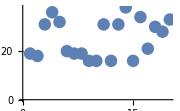

{19,18,31,36,32,20,19,19,16,16,31,16,31,38,16,34,21,30,28,33}

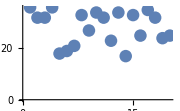

{36,32,32,36,18,19,21,33,27,34,32,23,34,17,33,25,35,32,24,25}

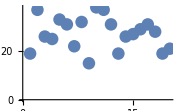

{19,37,26,25,33,31,22,32,15,38,37,31,19,26,27,29,31,28,19,21}

```mathematica
Table[
rints=RandomInteger[{15,38},20];
Print[littleplot[rints]];
Print[rints];
,3];
```

Seleção de uma série apropriada (temperatura).

```mathematica
temps1={17,19,19,33,22,37,21,37,35,29,15,22,21,20,21,29,23,24,29,20}
```

{17,19,19,33,22,37,21,37,35,29,15,22,21,20,21,29,23,24,29,20}

Geração de dados randômicos (frequentação).

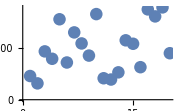

{3691,2546,7530,6377,12533,5798,10487,8767,6875,13338,3344,3145,4265,9254,8716,5068,14072,12979,14382,7244}

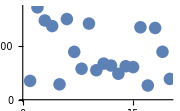

{2816,13814,11854,11023,2302,12069,7162,4636,11393,4410,5404,5113,3887,5011,4883,10841,2130,10737,7172,3111}

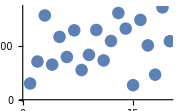

{2424,5701,12574,5241,9374,6377,10351,4433,6697,10407,5862,8761,12941,10609,2171,11910,8108,3735,13774,8732}

```mathematica
Table[
rints=RandomInteger[{2000,15000},20];
Print[littleplot[rints]];
Print[rints];
,3];
```

Escolha de uma série apropriada (frequentação).

```mathematica
pesss1={10699,10068,2188,13289,8568,6293,11939,11772,4992,11709,13684,4809,12308,2049,9088,13121,4795,12534,10353,4096}
```

{10699,10068,2188,13289,8568,6293,11939,11772,4992,11709,13684,4809,12308,2049,9088,13121,4795,12534,10353,4096}

```mathematica
Max[temps1]
```

37

```mathematica
Max[pesss1]
```

13684

Relativizar... à esquerda absoluto e à direita relativo.

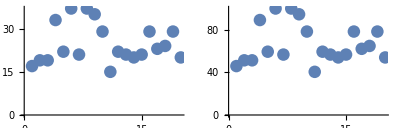

```mathematica
GraphicsRow[{littleplot[temps1],littleplot[N[temps1/Max[temps1]*100]]}]
```

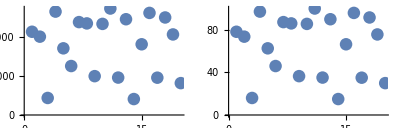

```mathematica
GraphicsRow[{littleplot[pesss1],littleplot[N[pesss1/Max[pesss1]*100]]}]
```

Comparação dos relativos (correlação visual).

```mathematica
temps1r=N[temps1/Max[temps1]*100];
pesss1r=N[pesss1/Max[pesss1]*100];
```

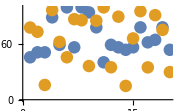

```mathematica
littleplot[{temps1r,pesss1r}]
```

Outra série de temperaturas.

```mathematica
temps2={26,31,25,22,33,16,22,19,36,17,37,23,36,24,22,27,21,15,36,35}
```

{26,31,25,22,33,16,22,19,36,17,37,23,36,24,22,27,21,15,36,35}

Diferença das temperaturas da média.

```mathematica
temps2v1=N[temps2-Mean[temps2]]
```

{-0.15,4.85,-1.15,-4.15,6.85,-10.15,-4.15,-7.15,9.85,-9.15,10.85,-3.15,9.85,-2.15,-4.15,0.85,-5.15,-11.15,9.85,8.85}

Diferença da média ao quadrado (variância):

```mathematica
temps2v2=N[(temps2-Mean[temps2])^2]
```

{0.0225,23.5225,1.3225,17.2225,46.9225,103.023,17.2225,51.1225,97.0225,83.7225,117.723,9.9225,97.0225,4.6225,17.2225,0.7225,26.5225,124.323,97.0225,78.3225}

Dados absolutos, diferença e variância:

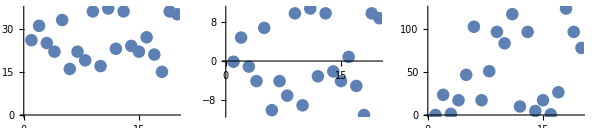

```mathematica
GraphicsRow[{littleplot[temps2],littleplot[temps2v1],littleplot[temps2v2]}]
```

Relativização (?) Usada abaixo.
1) Razões dos números para as médias, ×100 (médias centradas em 100).
2) Diferença destes números para as médias.
3) Diferença destes números para as médias, ao quadrado (variância).

O desvio padrão não usou para nada, mas a variância foi plotada das duas variáveis abaixo.

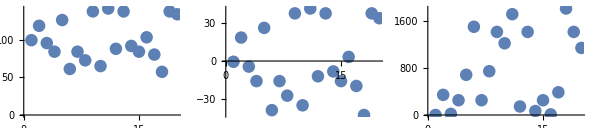

```mathematica
temps2r=temps2/Mean[temps2]*100;
temps2rv1=temps2r-Mean[temps2r];
temps2rv2=(temps2r-Mean[temps2r])^2;
GraphicsRow[{littleplot[temps2r],littleplot[temps2rv1],littleplot[temps2rv2]}]
```

```mathematica
Mean[temps2r]
```

100

Plot das distâncias relativizadas (distâncias dos valores de cada variável centrados em um valor em comum — 100 — para as médias destes valores).
Relativização de duas médias para comparação “absoluta” das diferenças.

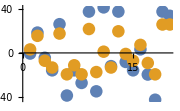

```mathematica
Clear[pesss2];
pesss2={
	5000,5600,4500,4200,5700,
	3900,4300,3900,5900,4000,
	4900,4200,5800,4800,4500,
	5200,4400,3900,6100,6100
};
pesss2r=pesss2/Mean[pesss2]*100;
pesss2rv1=N[pesss2r-Mean[pesss2r]];
littleplot[{temps2rv1,pesss2rv1}]
```

Com isso conseguimos comparar as diferenças da média dos dados com uma escala em comum.

```mathematica
Mean[pesss2r]
```

100

Calcular Pearson.

```mathematica
Clear[x,y];
x=temps2;
y=pesss2;
n=20;
```

```mathematica
x
```

{26,31,25,22,33,16,22,19,36,17,37,23,36,24,22,27,21,15,36,35}

```mathematica
{Total[x],Total[y],Total[x^2],Total[y^2],Total[x*y]}
```

{523,96900,14691,481070000,2633400}

```mathematica
N[(n*Total[x*y]-Total[x]*Total[y])/(√((n*Total[x^2]-Total[x]^2)*(n*Total[y^2]-Total[y]^2)))]
```

0.917278

```mathematica
fpearson[n_,x_,y_]:=(n*Total[x*y]-Total[x]*Total[y])/(√((n*Total[x^2]-Total[x]^2)*(n*Total[y^2]-Total[y]^2)))
```

```mathematica
N[fpearson[20,temps2,pesss2]]
```

0.917278

```mathematica
N[fpearson[20,temps1,pesss1]]
```

0.108658